```mathematica
Manipulate[
Module[{eq1,eq2,eq3,T1,T2},
eq1=200;
eq2=300;
eq3=350;

(*sol=Solve[
eq4=a*x^2+b*x+c;*)

T1=heat+150;
T2=T1-50;

If[x<0.6,{
If[step==0∧T1<eq1,{T=T1,step=0}],
If[step==0∧T1≥eq1∧T2≤eq1,{T=eq1,step=10}],
If[step==10,T=eq1],
If[(step==10∨step==2)∧T2>eq1,{T=T2,step=1}],(*allows for if above red line then move pt lower than 0.6.... to go lower than blue line*)
If[step==1,T=T2],
(*down*)
If[step==1∧T1≥eq1∧T2≤eq1,{T=eq1,step=10}],
If[step==10∧T1<eq1,{T=T1,step=0}]
}];
If[x>0.6,{
If[step==0∧T1<eq2,{T=T1,step=0}],
If[step==0∧T1≥eq2∧T2≤eq2,{T=eq2,step=20}],
If[step==20,T=eq2],
If[(step==20∨step==1)∧T2>eq2,{T=T2,step=2}],
If[step==2,T=T2],
(*down*)
If[step==2∧T1≥eq2∧T2≤eq2,{T=eq2,step=20}],
If[step==20∧T1<eq2,{T=T1,step=0}]
}];
(*If[x==0.6,{
If[step==0∧T1<3,{T=T1,step=0}],
If[step==0∧T1≥eq2∧T2≤eq2,{T=eq2,step=20}],
If[step==20,T=eq2],
If[(step==20∨step==1)∧T2>eq2,{T=T2,step=2}],
If[step==2,T=T2],
(*down*)
If[step==2∧T1≥eq2∧T2≤eq2,{T=eq2,step=20}],
If[step==20∧T1<eq2,{T=T1,step=0}]
}];*)

Graphics[{
Text[Framed[Style[Grid[{{"T =",T},{"step =",step}}],16],Background->LightYellow],{0.175,370}],
{Opacity[0.2,Blue],Rectangle[{0,100},{0.6,eq1}]},
{Opacity[0.2,Red],Rectangle[{0.6,100},{1,eq2}]},
{Thick,Blue,Line[{{0,eq1},{0.6,eq1}}],Red,Line[{{0.6,eq2},{1,eq2}}],Black,Line[{{0.6,100},{0.6,eq3}}]},
Inset[Graphics[{EdgeForm[Thick],Green,Polygon[{{0,0},{1,1},{0,2},{-1,1}}]},ImageSize->14],{0.6,eq2}],
{PointSize[0.0275],Point[{x,T}]}
},Frame->True,AspectRatio->1,PlotRange->{{0,1},{100,400}},FrameLabel->{Style["composition",16],Style["temperature",16]},LabelStyle->Black]
],
Grid[{
{Control[{{x,0.3,"composition"},0.01,0.99,0.01,Appearance->"Labeled"}],Button["reset to initial conditions",{x=0.3,heat=0,step=0,T=150}]},
{Control[{{heat,0,"add heat"},0,245,1,Appearance->"Labeled"}],
Control[{{step,0},0,100,None}],
Control[{T,150,None}]}
}]
]
```

Point starts in blue region (heat=0; T=150). If 50 units of heat (call it kJ for simplicity), the point must remain at T = 200 for a defined heat input/bound (say as another 50 kJ are added with slider) once the additional 50 kJ of heat have been added, the point can now rise (increase temperature). Currently this operation is achieved as follows:

Make controls for two new variables: step and T

```mathematica
Control[{{step,0},0,100,None}]
Control[{T,150,None}]
```

I use step to define each region the point is in, based on the conditions just before it’s current location (for example if step = 10, the point is sitting at 200 until enough heat is added). T 		describes the y-coordinate of the point, but it is defined in the code based on step, etc.

	Here is how T is actually defined, someone I worked with came up with this a while ago and I just have not found another way to achieve the behavior descibed above.
	For the light-blue region (x<0.6), I use several If statements and two more variables to set-up the conditions for when heat is added, but y-coordinate of the point does not change:

```mathematica
T1=heat+150;
T2=T1-50;
```

T1 is the initial location of the point (heat =0), T2 says that I want 50 kJ to be added before the temperature changes.

```mathematica
If[x<0.6,{
If[step==0∧T1<200,{T=T1,step=0}],(*initially, t-coord of point is T1*)
If[step==0∧x<0.6∧T1≥200∧T2≤200,{T=200,step=10}],(*for a range of 'heat' y-cood doesn't change*)
If[step==10,T=200],
If[step==10∧T2>200,{T=T2,step=1}],
If[step==1,T=T2],
(*then coming straight down to initial location*)
If[step==1∧T1≥200∧T2≤200,{T=200,step=10}],
If[step==10∧T1<200,{T=T1,step=0}]
}];
```

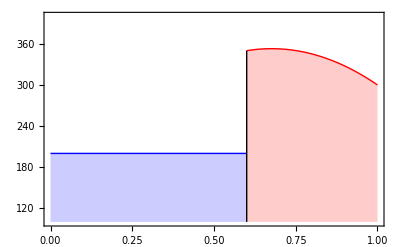

```mathematica
Module[{eq1,eq2,x1,y1,x2,y2,x3,y3,s,A,B,C,eq3},
eq1=200;
eq2=300;

x1=0.6;y1=350;
x2=0.83;y2=341;
x3=1;y3=300;

s=Quiet@Solve[a*x1^2+b*x1+c==y1&&a*x2^2+b*x2+c==y2&&a*x3^2+b*x3+c==y3,{a,b,c}][[1]];

A=a/.s;
B=b/.s;
C=c/.s;

eq3[x_]=A*x^2+B*x+C;

Show[
Plot[eq3[x],{x,0.6,1},PlotStyle->{Thick,Red},Filling->100,FillingStyle->Opacity[0.2,Red]],
Graphics[{
{Opacity[0.2,Blue],Rectangle[{0,100},{0.6,eq1}]},
(*{Opacity[0.2,Red],Rectangle[{0.6,100},{1,eq2}]},*)
{Thick,Blue,Line[{{0,eq1},{0.6,eq1}}],Black,Line[{{0.6,100},{0.6,eq3[0.6]}}]}
}],
Frame->True,ImageSize->400,PlotRange->{{0,1},{100,400}},Axes->False]
]
```